```mathematica
ClearAll["Global`*"]
```

```mathematica
L=1;
h=1;
c={0.5,0.5};
a=0.2;
b=0.1;
```

```mathematica
threshold=1*^-1;
```

```mathematica
u[x_]:={x[[1]],x[[2]]}
xref[s_]:=c+{a Cos[2 π s],b Sin[2 π s]}
xcur[s_]:=xref[s]+u[xref[s]]
nref[s_]:=1/Norm[xref'[s]]*{xref'[s][[2]],-xref'[s][[1]]}
ncur[s_]:=-1/Norm[xcur'[s]]*{xcur'[s][[2]],-xcur'[s][[1]]}
```

```mathematica
tt=Import["/Users/michelecastellana/Documents/finite_elements/fluid_structure_interaction/fluid_obstacle/monolithic/solution/snapshots/csv/n_cur.csv"];
```

```mathematica
For[t={};i=2,i<=Length[tt],i++,
If[Norm[{tt[[i,1]],tt[[i,2]]}]>threshold,AppendTo[t,tt[[i]]]]
]
```

```mathematica
t
```

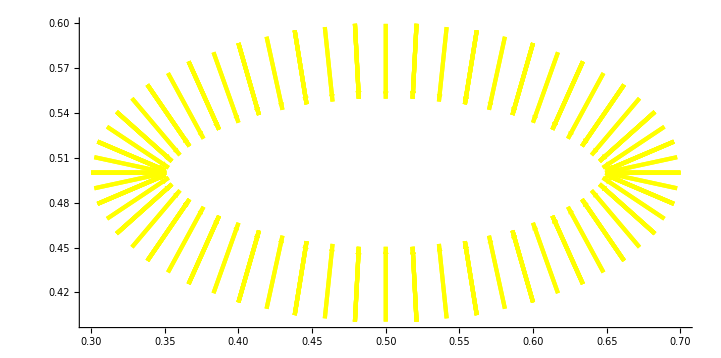

```mathematica
plotnrefcurnum = Graphics[
  {
   {Yellow, Arrowheads[0.02],AbsoluteThickness[3],
    Table[Arrow[{{t[[i,3]],t[[i,4]]}, {t[[i,3]],t[[i,4]]} + 0.05 {t[[i,1]],t[[i,2]]}}],{i, 1, Length[t]}]}
   },
  Axes -> True, AspectRatio -> Automatic
 ]
```

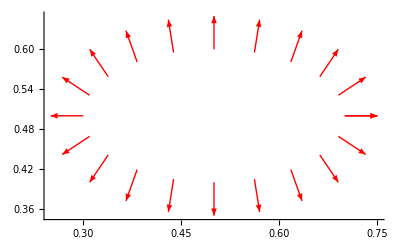

```mathematica
plotnref = Graphics[
  {
   (* normal vectors at sample points *)
   {Red, Arrowheads[0.02],
    Table[Arrow[{xref[s], xref[s] + 0.05 nref[s]}], {s, 0, 1, 0.05}]}
   },
  Axes -> True, AspectRatio -> Automatic
 ]
```

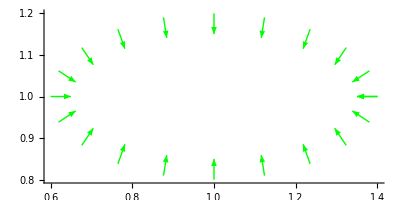

```mathematica
plotncur= Graphics[
  {
   (* normal vectors at sample points *)
   {Green, Arrowheads[0.02],
    Table[Arrow[{xcur[s], xcur[s] + 0.05 ncur[s]}], {s, 0, 1, 0.05}]}
   },
  Axes -> True, AspectRatio -> Automatic
 ]
```

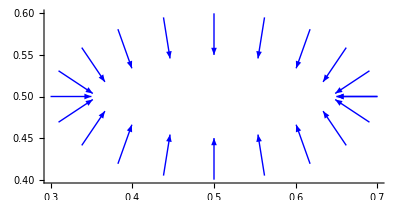

```mathematica
plotnrefcur= Graphics[
  {
   (* normal vectors at sample points *)
   {Blue, Arrowheads[0.02],
    Table[Arrow[{xref[s], xref[s] + 0.05 ncur[s]}], {s, 0, 1, 0.05}]}
   },
  Axes -> True, AspectRatio -> Automatic
 ]
```

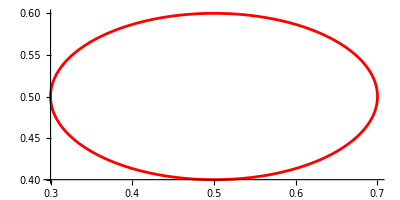

```mathematica
plotxref=ParametricPlot[xref[s],{s,0,1},PlotStyle->Red]
```

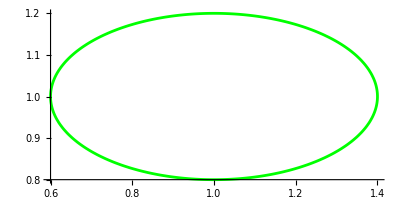

```mathematica
plotxcur=ParametricPlot[xcur[s],{s,0,1},PlotStyle->Green]
```

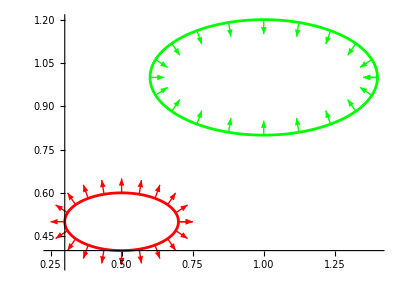

```mathematica
Show[plotxref,plotxcur,plotnref,plotncur,PlotRange->Full]
```

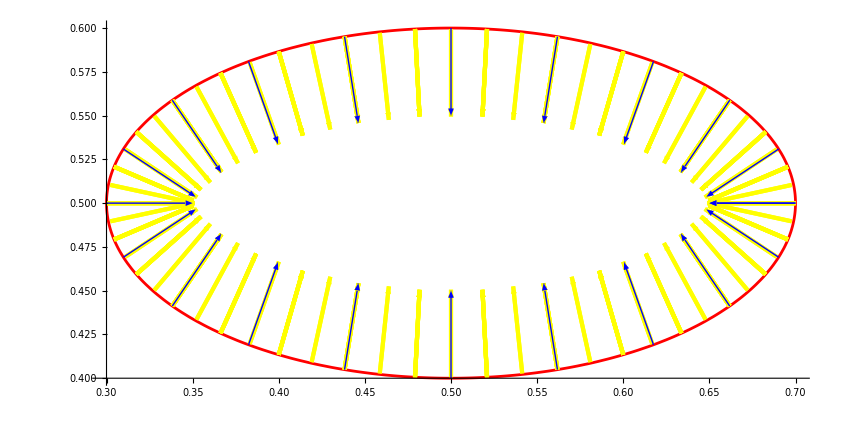

```mathematica
Show[plotxref,plotnrefcurnum,plotnrefcur,PlotRange->Full]
```